```mathematica
RandomInteger[{1,4}]
```

4

```mathematica
3.13-.8
```

2.33

```mathematica
3.13*.8
```

2.504

```mathematica
3.13+.8
```

3.93

```mathematica
3.13/.8
```

3.9125

```mathematica
Sin[Pi/6.]
```

0.5

```mathematica
Cos[Pi/6.]
```

0.866025

```mathematica
Clear[a]
c=1;
b=1/2;
f[x_]=(x+7)(a x^2+b x+c);
Expand[f[x]]
```

7+(9 x)/2+x^2/2+7 a x^2+a x^3

```mathematica
Solve[f'[-7] == 3/7]
```

{{a→41/686}}

41/686

7+(9 x)/2+(45 x^2)/49+(41 x^3)/686

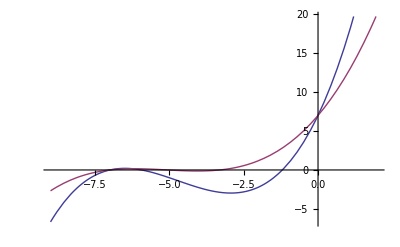

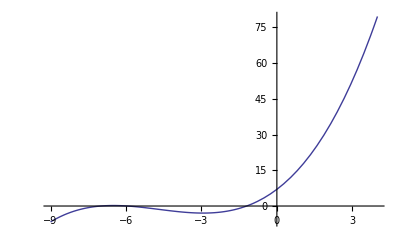

```mathematica
a=41/686
Expand[f[x]]
Plot[{7+8 x+(97 x^2)/49+(48 x^3)/343,f[x]},{x,-9,2}]
```